# Analyzing Motors

Robert Atkinson

2018.07.10

## Loess Regression Infrastructure

The Loess algorithm is an algorithm for fitting a smooth curve to a (noisy) data set without having to a priori choose the form of the smoothing functions (e.g., polynomial, exponential, etc.) used to fit the data. Briefly, the algorithm functions as follows:

We will visit the data at a number of fit points. Classically, the fit points have simply been the x values of the data set; however, good results seem to be also achieved with using somewhat fewer equally spaced points across the domain.

At each of the fit points, we determine a neighborhood of the data. The neighborhood of a fit point xCenter is the set of size k of the x values from the data which are the closest to xCenter. The value k is usually expressed as a particular fraction α of the overall data.

There is no hard and fast rule, but values for α around 0.5 often produce good results. If too small a value is used, the Loess smoothed fit will follow the data too closely; if too large a value is used, intermediate variations in the data might be missed.

We perform a weighted least squares regression of each fit neighborhood.

The regression is not necessarily a linear one; rather, we fit a polynomial (of a fixed maximal degree) to the fit neighborhood. Typical values used for the maximal degree are 1 and 2.

The weighting function used assigns greater importance to the center of the the neighborhood than its edges.

With regressed polynomial in hand for the neighborhood of a particular fit point x_i we evaluate the polynomial at x_ito yield y_i, which becomes the value of the Loess smoothed fit at x_i.

The value the Loess smoothed fit at a location which falls between fit points is determined by interpolating between the (x_i,y_i) points, typically using either cubic splines or straight lines for the interpolation.

References: 
	Cleveland, W. S. Robust Locally Weighted Regression and Smoothing Scatterplots. Journal of the American Statistical Association 74, 829, doi:10.2307/2286407 (1979).
	http://en.wikipedia.org/wiki/Local_regression

### Fit points

We have two ways we can determine which points we use for fitting The first, which seems to be the traditional way, is to fit at each point at which we actually have data. The second is to space a number of points (possibly far fewer than the number of samples) equally across the domain of the data (we force the inclusion of the extremes so as to definitely cover the whole domain of the data). In practice, the two approaches seem to have very similar results if the data is dense.

```mathematica
deleteDuplicates[data_] := DeleteDuplicates[data, Abs[#1 -#2] < 10^-9&]
fitPoints[data_, interpolationFraction_] := Block[{min=data[[All,1]]// Min, max=data[[All,1]]// Max}, 
If [0 == interpolationFraction,
data[[All,1]] // deleteDuplicates // Sort,
Union[
Range[min, max, (max-min)/Max[3, Length[data]* interpolationFraction]],  
{min,max}] // deleteDuplicates // Sort
]]
fitPoints[data_] := fitPoints[data, 0]
```

### Neighborhood

We define a function that computes the neighborhood of a given point using a particular fraction of the data.

```mathematica
neighborhoodIndices[data_, xCenter_, α_] :=Block[{n},
n = Min[Length[data], Ceiling[α * Length[data]]];
Ordering[Abs[#[[1]]-xCenter] & /@ data, n] // Sort];
```

```mathematica
dataNeighborhood[data_, xCenter_, α_] := data[[neighborhoodIndices[data, xCenter, α]]]
```

### Weight function

The tricube function is the weighting function typically used in Loess smoothing, though other approaches are possible.

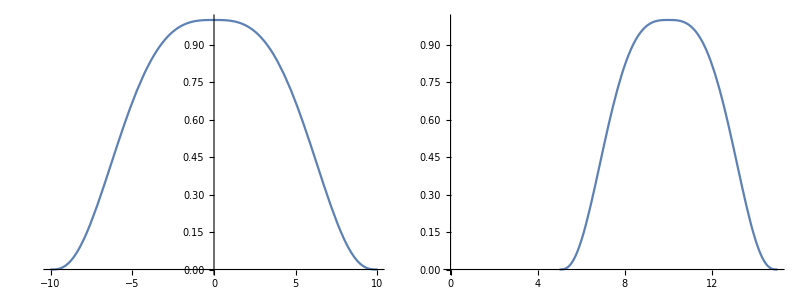

```mathematica
tricube = Compile [{u}, If[Abs[u]<1,(1-Abs[u]^3)^3,0]];
tricubeRange = Compile[{u, uCenter, uHalfWidth}, Block[{uMin = uCenter - uHalfWidth},  tricube[ (u-uMin) / (uHalfWidth * 2) * 2 - 1]]];
{{Plot[tricubeRange[x, 0,10], {x, -10, 10}, AxesOrigin-> {0,0}],
Plot[tricubeRange[x, 10,5], {x, 5, 15}, AxesOrigin-> {0,0}]} }// TableForm
```

### Weights for neighborhood

We define a function that computes the weights for a range of data; in practice, we will apply this to subsets of data corresponding to fit neighborhoods.

```mathematica
weights[data_, xCenter_, α_] := Block[{xMin, xMax, xHalfWidth},
 xMin=data[[1,1]]; xMax=data[[Length[data], 1]];
xHalfWidth = Max[xCenter -xMin, xMax - xCenter];
tricubeRange[#[[1]], xCenter, xHalfWidth]&/@ data]
```

### Regression

We define a function that performs the regression at a particular fit point, then a second function which iterates over all such points.

```mathematica
regressAtX[data_, x_, α_, degree_] := Block[{y, hood, fit},
hood = dataNeighborhood[data, x, α];
fit = LinearModelFit[hood, y^Range[0,degree], y,Weights -> weights[hood, x, α]];
fit["BestFit"]/. y -> x]
```

The regress function returns the (x_i,y_i) pairs of the smoothed fit. This is the main function one calls to carry out a regression. The first parameter is the data, the second parameter is the fraction of the data to use in generating each neighborhood, the third parameter is the degree of interpolation polynomials to use in each neighborhood, and the last parameter controls which fit points are used: zero indicates use the data points as fit points, while a nonzero value indicates that the specified fraction of the number of data points are to be used as equally spaced fit points across the range of the data.

```mathematica
regress[unsortedData_, α_, degree_, interpolationFraction_] := Block[{sortedData, result, xx},
sortedData = Sort[unsortedData, #1[[1]] < #2[[1]]&];
result = { #, regressAtX[sortedData, #, α, degree] }& /@ fitPoints[sortedData, interpolationFraction];
result]
```

### Example

As a test example of algorithm, we generate some noisy data from the Sin[] function.

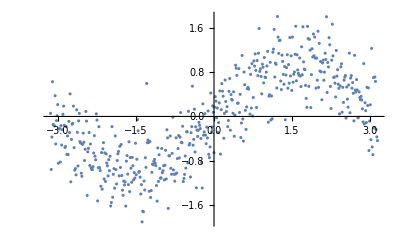

```mathematica
xx = N[Range[-Pi, Pi, 2 Pi / 500]];
yy = Sin[#] + 0.4RandomVariate[NormalDistribution[]]& /@ xx;
data = Transpose[{xx, yy}];
ListPlot[data]
```

Run a regression on our sample test data. We use half the data for each neighborhood, degree 2 polynomials for each regression, and all our data as equally spaced fit points (again, this is what the 0 parameter at the end means).

```mathematica
regression  = regress[data, 0.5, 2, 0];
```

To construct a cubic spline fit from the fit points, we use Mathematica’s built-in Interpolation function. We then plot the data and our fitting thereto.

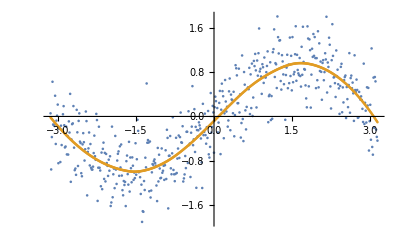

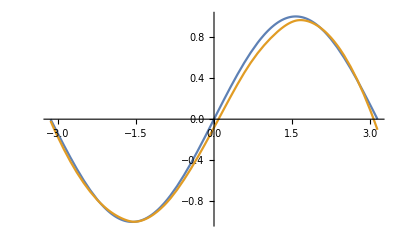

```mathematica
loessInterp = Interpolation[regression, InterpolationOrder-> 3];
ListPlot[{data, regression}]
Plot[{Sin[x],loessInterp[x]}, {x, -Pi, Pi}]
```

## Laplace Transform of Experimental Data

Next, we explore the creation of Laplace transforms of experimental data. Our approach will be to piecewise compute the exact Laplace transform over a polynomial fitted on each of the segments of the data, then sum over all such segments to compute the Laplace transform of the data as a whole.

#### Manipulating Interpolating Functions

We begin with some mechanisms for manipulating interpolations. The first one is a bit of a mouthful, but it seems to work.

```mathematica
(* from https://mathematica.stackexchange.com/questions/59944/extracting-the-function-from-interpolatingfunction-object *)
convertToPiecewise::umet="Unknown interpolation method `1`.";
SetAttributes[convertToPiecewise,Listable];

convertToPiecewise[iF_InterpolatingFunction,x_,OptionsPattern[{"Extrapolation"->False,InterpolationOrder->Automatic}]]:=Module[{bf,extQ,imet,kp,makePP,met,nodes,perQ,pieces,pts,vand,xt},Switch[met=iF["InterpolationMethod"],"Hermite"|"Chebyshev",pts=Transpose[{Flatten[iF["Grid"]],iF["ValuesOnGrid"]}],"BSpline",bf=First[Cases[iF,_BSplineFunction,∞]];
pts={#,bf[#]}&/@Union[First[bf["Knots"]]],_,Message[convertToPiecewise::umet,met];Return[$Failed,Module]];
kp=OptionValue[InterpolationOrder];
If[kp===Automatic,(*repeated differentiation to determine maximal order*)kp=First[NestWhile[Derivative[1],Derivative[First[iF["InterpolationOrder"]]+1][iF],(Norm[#["ValuesOnGrid"],∞]>0)&]["DerivativeOrder"]]-1];
If[kp>0,(*normal case*)(*use equispaced nodes in the exact case,and Chebyshev otherwise*)nodes=Range[kp-1]/kp;
If[MatrixQ[pts,InexactNumberQ],nodes=N[Haversine[π nodes],Precision[pts]]];
vand=LinearAlgebra`Private`VandermondeSolve[##,Transpose->True]&;
makePP[{{x1_,y1_},{x2_,y2_}}]:=Module[{h=x2-x1,ip},ip=Transpose[Join[{{x1-x1,y1}},{#,iF[x1+#]}&/@(h nodes),{{h,y2}}]];
(*solve for interpolating polynomial coefficients*){Fold[(#1 (xt-x1)+#2)&,Reverse[vand@@ip]],x1≤xt≤x2}];
pieces=makePP/@Partition[pts,2,1],(*zero-order interpolation*)pieces=Transpose[{Rest[pts[[All,-1]]],#1≤xt≤#2&@@@Partition[pts[[All,1]],2,1]}]];
perQ=TrueQ[First[iF["Periodicity"]]];
If[!perQ,extQ=OptionValue["Extrapolation"];
If[!ListQ[extQ],extQ={extQ,extQ}];extQ=TrueQ/@extQ;
If[extQ[[1]],pieces[[1,2]]=Delete[pieces[[1,2]],1]];
If[extQ[[2]],pieces[[-1,2]]=Delete[pieces[[-1,2]],3]]];
Piecewise[pieces/.xt->If[!perQ,x,Mod[x,#2-#1,#1]&@@First[iF["Domain"]]]]]
```

getPolynomials[] returns a list of triplets, each a pair of bounding x values followed by a polynomial used  by the interpolation function within those bounds.

```mathematica
getPolynomials[if_InterpolatingFunction, t_] := Module[{pw, coords, bounds},
pw = convertToPiecewise[if, t];
coords = if["Coordinates"][[1]];
bounds = {coords[[#]], coords[[#+1]]} & /@ Range[1, Length[coords]-1];
{#[[1]], #[[2]], Refine[pw, #[[1]] < t && t ≤ #[[2]]]} & /@ bounds]
```

sampleFunction[] is a handy utility for evaluating a function at a set of desired data points. It is useful for making tests.

```mathematica
sampleFunction[fn_, xmin_, xmax_, n_] := Module[{xValues, yValues},
xValues = Range[xmin, xmax, (xmax-xmin) / n];
yValues = fn /@ xValues;
{xValues, yValues} // Transpose]
```

#### Some Tests

A short test.

```mathematica
testfn = Sin[5 #] UnitStep[#] &
testInterp = Interpolation[sampleFunction[testfn, -2, 10, 400] // N]
Take[getPolynomials[testInterp, t], -10] // ColumnForm
```

Sin[5 #1] UnitStep[#1]&

InterpolatingFunction[…]

{9.7,9.73,-0.981108+(-0.965902+(12.2409+2.48052 (-9.7+t)) (-9.7+t)) (-9.7+t)}
{9.73,9.76,-0.999002+(-0.221953+(12.4641-0.629668 (-9.73+t)) (-9.73+t)) (-9.73+t)}
{9.76,9.79,-0.99446+(0.526981+(12.4075-3.72572 (-9.76+t)) (-9.76+t)) (-9.76+t)}
{9.79,9.82,-0.967584+(1.26408+(12.0721-6.7381 (-9.79+t)) (-9.79+t)) (-9.79+t)}
{9.82,9.85,-0.918979+(1.97279+(11.4657-9.59916 (-9.82+t)) (-9.82+t)) (-9.82+t)}
{9.85,9.88,-0.849735+(2.6372+(10.6018-12.2446 (-9.85+t)) (-9.85+t)) (-9.85+t)}
{9.88,9.91,-0.761408+(3.24238+(9.49977-14.6151 (-9.88+t)) (-9.88+t)) (-9.88+t)}
{9.91,9.94,-0.655982+(3.77474+(8.18441-16.6574 (-9.91+t)) (-9.91+t)) (-9.91+t)}
{9.94,9.97,-0.535823+(4.22233+(6.68524-18.3256 (-9.94+t)) (-9.94+t)) (-9.94+t)}
{9.97,10.,-0.403631+(4.57397+(5.03594-18.3256 (-9.97+t)) (-9.97+t)) (-9.97+t)}

#### Piece

piece[] constructs a function that is  zero everywhere except between two points. What happens between the two points is given by a provided function, which by default is just a straight line.

```mathematica
Clear[piece]
Options[piece] = {Before -> "Zero", After -> "Zero"};
piece[p1:{x1_, y1_}, p2:{x2_, y2_}, opts: OptionsPattern[]] :=piece[x1, x2, (y2-y1) / (x2 - x1) * (# -x1)  + y1 &, opts];
piece[x1_, x2_, fn_, opts: OptionsPattern[]] := Module[{g1, g2, before, after},
before = Switch[OptionValue[Before], "Constant", fn[x1], "Zero", 0, _, Message["invalid option"];0];
after = Switch[OptionValue[After], "Constant", fn[x2], "Zero", 0, _, Message["invalid option"];0];
g1[t_] := fn[t]  UnitStep[t - x1];
g2[t_] := fn[t]  UnitStep[t - x2]; 
g1[#] -  g2[#] + after UnitStep[# - x2] + before (1 - UnitStep[#-x1]) &]
```

Some examples:

{{x1,Piecewise[{{y1, x1<x2}, {0, True}}]},{x2,Piecewise[{{-y2, x1>x2}, {0, True}}]}}

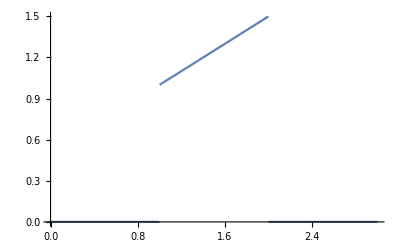

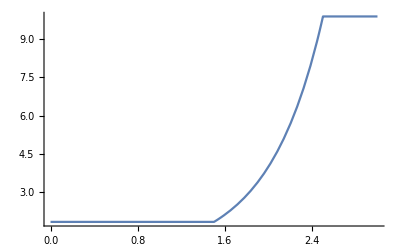

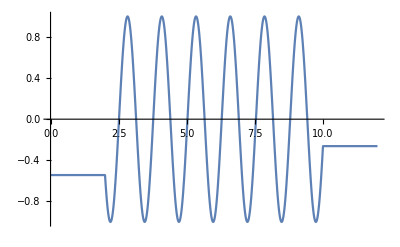

```mathematica
{#, piece[{x1, y1}, {x2, y2}][#]} & /@ {x1, x2}  // FullSimplify
Plot[piece[{1,1}, {2, 3/2}][x], {x, 0, 3}, AxesOrigin->{0,0}]
Plot[piece[1.5, 2.5, #^#&, Before -> "Constant", After-> "Constant"][x], {x, 0, 3}, AxesOrigin->{0,0}, PlotRange->All]
Plot[piece[2, 10, Sin[5 #]&, Before -> "Constant", After-> "Constant"][x], {x, 0, 12}, AxesOrigin->{0,0}, PlotRange->All]
```

#### Pieces

pieces[] outputs a piecewise function to model all the underlying data of an Interpolation.

```mathematica
Clear[pieces]
pieces[if_InterpolatingFunction] := Module[{polys, t},
polys  = getPolynomials[if, t]; 
piece[#[[1]], #[[2]], Function[tt, #[[3]] /. t-> tt]]& /@ polys
]
```

A utility for plotting a set of pieces as a whole, with a test thereof.

```mathematica
ppTestInterp = pieces[testInterp];
```

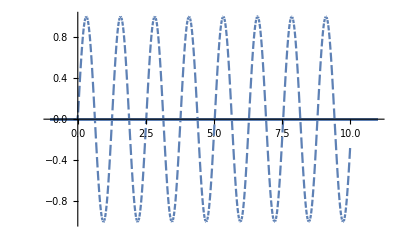

```mathematica
Clear[plotPieces]
plotPieces[pp_, x1_, x2_] := Module[{t},
Show[Plot[#[t], {t, x1, x2}, PlotRange->All] & /@ pp]
]
plotPieces[ppTestInterp, -1, 11]
```

#### Laplace Transform

laplaceTransform[] takes the output of Interpolation or just a raw dataset itself and returns a function which evaluates the Laplace Transform of that data. 

compiledLaplaceTransform[] functions identically, but is compiled to machine code and is thus considerably faster.

```mathematica
Clear[laplaceTransform, compiledLaplaceTransform]
Options[laplaceTransform] = {Before -> "Zero", After -> "Zero", Plot-> False, InterpolationOrder -> 1};
Options[compiledLaplaceTransform] = Options[laplaceTransform];

laplaceTransform[if_InterpolatingFunction, opts: OptionsPattern[]] := Module[{domain, x1, x2, before, after, pp, xforms, t, s, xform},
domain = if["Domain"][[1]];
x1 = domain[[1]];
x2 = domain[[2]];
before = Switch[OptionValue[Before], "Constant", if[x1], "Zero", 0, _, Message["invalid option"];0];
after = Switch[OptionValue[After], "Constant", if[x2], "Zero", 0, _, Message["invalid option"];0];
pp = pieces[if]
~Join~ { after UnitStep[# - x2] + before (1 - UnitStep[#-x1]) &};
If[OptionValue[Plot], Print[plotPieces[pp, x1 - (x2-x1) / 5, x2 + (x2-x1) / 5]]];
xforms = (Simplify[LaplaceTransform[#[t], t, s]]& /@ pp);
xform = Total[xforms];
xform /. s -> #&]
laplaceTransform[data_List, opts: OptionsPattern[]] := Module[{if},
if = Interpolation[data, InterpolationOrder-> OptionValue[InterpolationOrder]];
laplaceTransform[if,opts]
]

compiledLaplaceTransform[if_InterpolatingFunction, opts: OptionsPattern[]] := Module[{lp},
lp = laplaceTransform[if, opts];
Compile[{{ss, _Complex}}, Evaluate[lp[ss]]]
]
compiledLaplaceTransform[data_List, opts: OptionsPattern[]] := Module[{if},
if = Interpolation[data,  InterpolationOrder->OptionValue[InterpolationOrder]];
compiledLaplaceTransform[if, opts]
]
```

#### Tests

Even the symbolic truncation affects the result of the Laplace transform.

{-2.,10.}

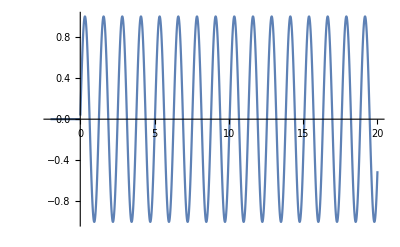

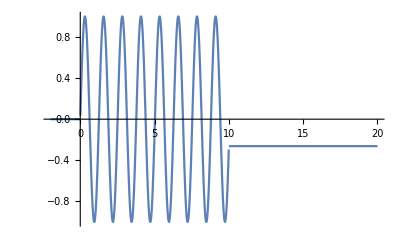

```mathematica
dom = testInterp["Domain"][[1]]
x1 = dom[[1]]; x2 = dom[[2]];
testfnPiece = piece[x1, x2,testfn, After -> "Constant"];
Plot[testfn[x], {x, x1, 2 x2}]
Plot[testfnPiece[x], {x, x1, 2 x2}]
```

5/(25+s^2)

-(0.262375 ⅇ^(-10. s))/s+5/(25+s^2)-(ⅇ^(-10. s) (4.82483-0.262375 s))/(25.+s^2)

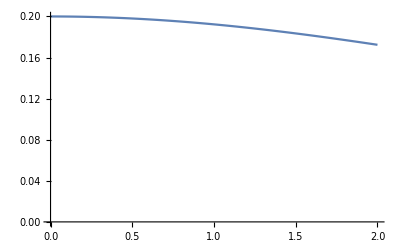

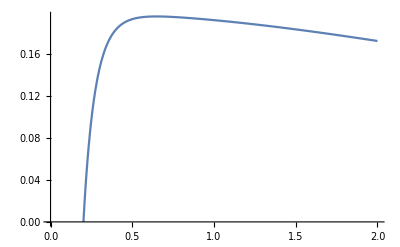

```mathematica
lpTestFn = LaplaceTransform[testfn[t], t, s]
lpTestfnPiece = LaplaceTransform[testfnPiece[t], t, s]
Plot[lpTestFn, {s, 0, 2}, AxesOrigin->{0,0}]
Plot[lpTestfnPiece, {s, 0, 2}, AxesOrigin->{0,0}]
```

We compare three different ways of calculating the Laplace transform of the piece: Symbolically, interpreted, and compiled. They should all match. And they do, quite well, as you can see when we overlay them below.

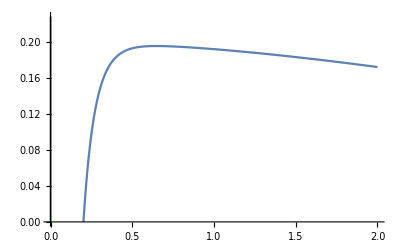
{-Graphics-,-Graphics-,-Graphics-}

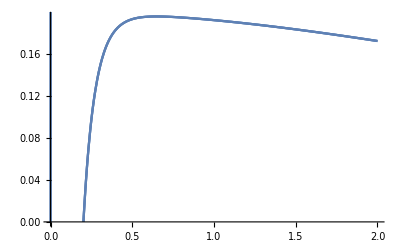

```mathematica
lp = laplaceTransform[testInterp, After -> "Constant"];
clp = compiledLaplaceTransform[testInterp, After -> "Constant"];

p1 = Plot[lpTestfnPiece, {s, 0, 2}, AxesOrigin->{0,0}];
p2 = Plot[lp[s], {s, 0, 2}, AxesOrigin->{0,0}];
p3 = Plot[clp[s], {s, 0, 2}, AxesOrigin->{0,0}];
{p1, p2, p3}
Show[p1, p2, p3]
```

Ok, now let’s explore some 2D plots for comparison.

```mathematica
Clear[plotLaplaceTransform]
plotLaplaceTransform[fn_, sRange_] := plotLaplaceTransform[fn, sRange, sRange];
plotLaplaceTransform[fn_, reRange_, imRange_] := plotLaplaceTransform[fn, {-reRange, reRange}, {-imRange, imRange}]
plotLaplaceTransform[fn_, {rmin_, rmax_},{imin_, imax_}] := Module[{},
{
Plot3D[fn[x + I y] // Abs, {x, rmin, rmax}, {y, imin, imax}, ImageSize->Medium, MaxRecursion->9, AxesLabel->{"Re", "Im"}],
Plot3D[fn[x + I y] // Arg, {x, rmin, rmax}, {y, imin, imax}, ImageSize->Medium, MaxRecursion->6, AxesLabel->{"Re", "Im"}]
}
]
```

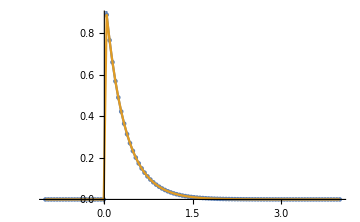
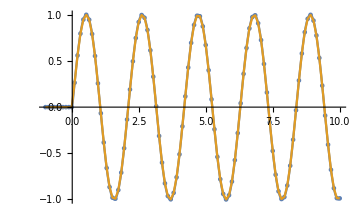
{{ⅇ^(-12-4 s)/s+1/(3+s)-ⅇ^(-4 (3+s))/(3+s),-Graphics-,{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}},{3/(9+s^2)+(ⅇ^(-10 s) Sin[30])/s-(ⅇ^(-10 s) (3 Cos[30]+s Sin[30]))/(9+s^2),-Graphics-,{-Graphics3D-,-Graphics3D-},{-Graphics3D-,-Graphics3D-}}}

```mathematica
Clear[testLaplaceTransform]
testLaplaceTransform[fn_, xmin_, xmax_, n_, sRange_] := Module[{after, fnPiece, symLp, symLpFn, xValues, yValues, data, tt, ss, clp2, if},
after = "Constant";
(* Compare apples to apples: clip the symbolic form to the same range we're going to sample *)
fnPiece = piece[xmin, xmax, fn, After -> after];
(* evaluate the symbolic form of the Laplace transform *)
symLp = LaplaceTransform[fnPiece[tt], tt, ss];
symLpFn = Function[{sss}, symLp /. ss -> sss];
(* sample the function and make an interpolation. data should be of even length *)
data = sampleFunction[fn, xmin, xmax, n] // N; 
if = Interpolation[data, InterpolationOrder->1]; 
(* compute its numeric Laplace transform *)
clp2 = compiledLaplaceTransform[if, After -> after];
(* plot both symbolic and numerical to compare *)
{symLpFn[s],
Show[
ListPlot[data, AxesOrigin-> {0,0}, ImageSize->Medium, PlotRange->All],  
Plot[{fnPiece[t],if[t]}, {t, xmin, xmax}, PlotRange->All] 
],
plotLaplaceTransform[symLpFn, sRange], 
plotLaplaceTransform[clp2, sRange]
}
]
Apply[testLaplaceTransform , #]& /@ {
{Exp[-3 #] UnitStep[#] &, -1, 4, 101, 2},
{Sin[3 #] UnitStep[#] &, -1, 10, 101, 2} 
}
```

That’s pretty sweet!

## Experimental Data

Let’s gather the experimental data together so we can manipulate it. Note: we need an even number of samples (it seems) to make the numerical Laplace transform work properly.

246

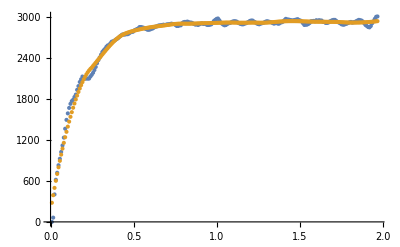

```mathematica
yValues = {0.0,62.5,402.77777777777777,617.1875,720.0,830.0,925.0,1025.0,1120.0,1235.0,1365.0,1495.0,1590.0,1670.0,1730.0,1770.0,1790.0,1830.0,1865.0,1935.0,1990.0,2050.0,2090.0,2130.0,2100.0,2100.0,2100.0,2100.0,2100.0,2130.0,2155.0,2185.0,2225.0,2270.0,2325.0,2370.0,2410.0,2450.0,2490.0,2515.0,2535.0,2565.0,2585.0,2590.0,2615.0,2640.0,2645.0,2655.0,2670.0,2680.0,2695.0,2715.0,2730.0,2745.0,2745.0,2745.0,2750.0,2750.0,2760.0,2775.0,2785.0,2785.0,2805.0,2815.0,2825.0,2835.0,2855.0,2855.0,2850.0,2845.0,2835.0,2825.0,2815.0,2815.0,2820.0,2830.0,2835.0,2850.0,2860.0,2865.0,2875.0,2880.0,2880.0,2885.0,2890.0,2885.0,2890.0,2895.0,2895.0,2900.0,2905.0,2900.0,2900.0,2885.0,2870.0,2870.0,2880.0,2880.0,2910.0,2925.0,2930.0,2930.0,2935.0,2925.0,2920.0,2920.0,2910.0,2900.0,2890.0,2895.0,2885.0,2895.0,2905.0,2910.0,2900.0,2905.0,2895.0,2885.0,2885.0,2890.0,2895.0,2920.0,2945.0,2960.0,2975.0,2980.0,2955.0,2925.0,2905.0,2890.0,2880.0,2885.0,2900.0,2910.0,2915.0,2925.0,2935.0,2940.0,2940.0,2935.0,2920.0,2910.0,2900.0,2895.0,2895.0,2905.0,2910.0,2920.0,2930.0,2945.0,2950.0,2950.0,2935.0,2925.0,2910.0,2900.0,2895.0,2905.0,2910.0,2915.0,2925.0,2935.0,2940.0,2935.0,2930.0,2925.0,2915.0,2905.0,2910.0,2915.0,2905.0,2905.0,2920.0,2925.0,2935.0,2955.0,2975.0,2965.0,2965.0,2960.0,2955.0,2950.0,2955.0,2960.0,2965.0,2970.0,2955.0,2950.0,2935.0,2910.0,2885.0,2890.0,2890.0,2900.0,2915.0,2940.0,2940.0,2945.0,2940.0,2955.0,2945.0,2955.0,2950.0,2950.0,2930.0,2930.0,2915.0,2915.0,2920.0,2935.0,2945.0,2955.0,2960.0,2960.0,2945.0,2930.0,2920.0,2910.0,2895.0,2890.0,2890.0,2900.0,2905.0,2915.0,2925.0,2930.0,2920.0,2925.0,2930.0,2940.0,2950.0,2960.0,2955.0,2950.0,2935.0,2910.0,2885.0,2870.0,2855.0,2850.0,2870.0,2910.0,2940.0,2975.0,3005.0,3010.0};
xValues = Range[0.008, 1.968, 0.008];
data = { xValues, yValues } // Transpose;
smoothedData = regress[data, 0.25, 2, 0];
Length[data]
ListPlot[{data, smoothedData}]
```

Compute the numerical Laplace transform and plot it.

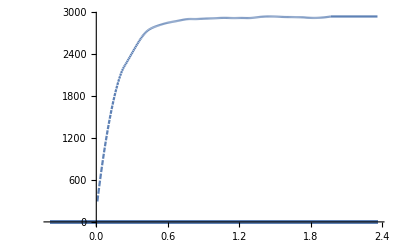

```mathematica
clp = compiledLaplaceTransform[smoothedData,  After -> "Constant", Plot -> True];
```

```mathematica
plotLaplaceTransform[clp, 4]
plotLaplaceTransform[1/ clp[#]&, 4]

plotLaplaceTransform[1/clp[#]&, {-2.765, -2.735}, {-4,4}]
```

{-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-}

{-Graphics3D-,-Graphics3D-}

Let’s examine vertical slices

```mathematica
Manipulate[
{Plot[clp[x + I y] // Abs, {y, -10,10}, AxesOrigin->{0,0}, ImageSize->Medium],
Plot[clp[x + I y] // Abs, {y, -100,100}, AxesOrigin->{0,0}, ImageSize->Medium, PlotRange->{0, 1}],
Plot[clp[x + I y] // Abs, {y, -100,100}, AxesOrigin->{0,0}, ImageSize->Medium]},
{{x, -2.9}, -4, 4}]
```

## Revision History

2018.8.27 Made some spelling and grammar edits.  Analyzed and made small adjustments to final graphs and Manipulate interactive.